```mathematica
GetExperimentID[expStr_]:=ToExpression[#]&/@StringSplit[expStr,"_"][[2;;All]]
SetDirectory["/Volumes/marshallShare/UCI/Yoosook/"];
(*Load Data*)
raw=Import["./thresholdCrosses.csv"];
clean=#[[1;;6]]&/@raw;
expTuples={GetExperimentID[#[[1]]],#[[2;;All]]}&/@clean;
paramsRanges=DeleteDuplicates[#]&/@(expTuples[[All,1]]//Transpose)
thresholds={.25,.50,.75,.90,.95};
(* Key: {releaseRatio, releasePattern, fitnessCost, standingVariation}*)
```

{{100,133,200,400,1000,1333,2000,4000,10000,20000,100000,250000,500000,1000000},{1,2,3,4,5,6,7,8,9,10,11,12,13},{100},{1,5,10,50,100,500,1000}}

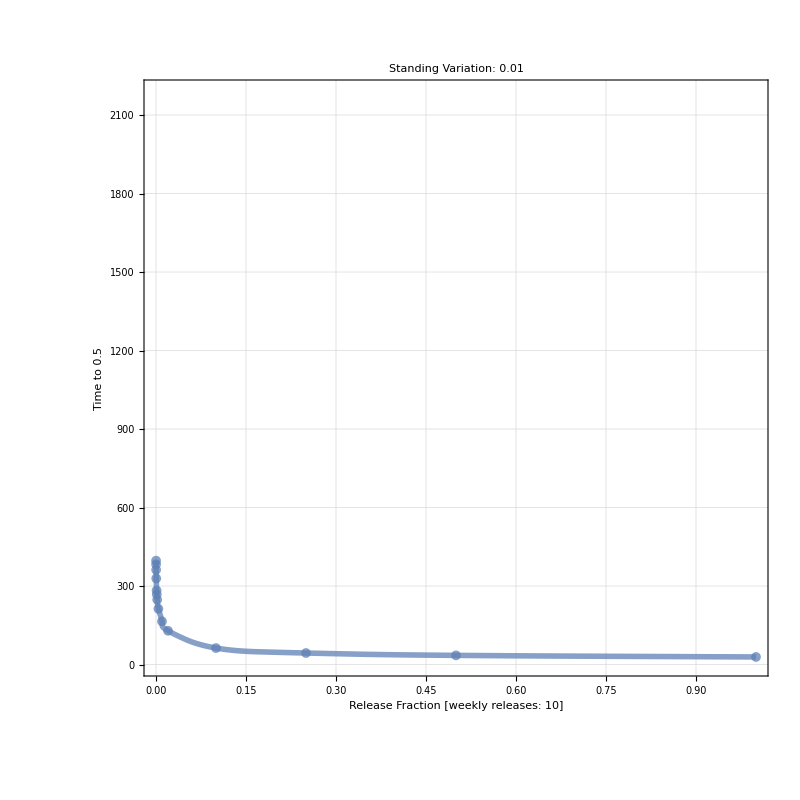

Export::nodir: Directory /Volumes/marshallShare/temp/nnTransfer/img/ does not exist.

Export::noopen: Cannot open ./img/CR_10_500_1000.png.

$Failed

```mathematica
{thresholdIx,releases,standingVar}={2,10,1000};
filtered=Cases[expTuples,{{_,releases,_,standingVar},_}];
tuples={#[[1,1]]/1000000,#[[2,thresholdIx]]}&/@filtered;
linePlot=ListLinePlot[tuples
,AspectRatio->1
,Frame->True
,FrameLabel->(Style[#,30]&/@{
"Release Fraction [weekly releases: " <> ToString[releases]<>"]", 
"Time to "<>ToString[thresholds[[thresholdIx]]]
})
,FrameStyle->Directive[Gray,Thick]
,GridLines->Automatic
,ImageSize->800
,InterpolationOrder->2
,PlotLabel->Style["Standing Variation: "<>ToString[(standingVar/100000)//N],30]
,PlotMarkers->{Automatic, 10}
,PlotRange->{{0,1},{0,6*365}}
,PlotStyle->Directive[Thickness[.005],Opacity[.75]]
,FrameTicksStyle->Directive[20]
]
Export[
"./img/CR_"<>ToString[releases]<>"_"<>ToString[Round[thresholds[[thresholdIx]]*1000]]<>"_"<>ToString[standingVar]<>".png"
,%
,ImageResolution-> 500
]
```